```mathematica
Quit[]
```

# MeV-DM: Scalar Mediator model

Load `HazmaTools`.Note that this will load `FeynCalc` and the patched `FeynArts`

```mathematica
Import[NotebookDirectory[]<>"../HazmaTools/HazmaTools.m"]
$HazmaModel="scalar";
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

MeV-DM - Scalar Mediator: version 1.0

by Adam Coogan and Logan A. Morrison

## Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
amplitudeLL=HazmaCreateAmplitude[{statex,statexbar},{statel,statelbar},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
amplitudeGG=HazmaCreateAmplitude[{statex,statexbar},{stateγ,stateγ}];
(* x + xbar-> pi0 + pi0 *)
amplitudeπ0π0=HazmaCreateAmplitude[{statex,statexbar},{stateπ0,stateπ0}];
(* x + xbar-> pi + pi *)
amplitudeπpπm=HazmaCreateAmplitude[{statex,statexbar},{stateπp,stateπm}];
(* x + xbar-> S + S *)
amplitudeSS=HazmaCreateAmplitude[{statex,statexbar},{states,states}];
```

## Squared Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
msqrdLL=HazmaCreateAmplitudeSquared[{statex,statexbar},{statel,statelbar},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
msqrdGG=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateγ,stateγ}];
(* x + xbar-> pi0 + pi0 *)
msqrdπ0π0=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateπ0,stateπ0}];
(* x + xbar-> pi + pi *)
msqrdπpπm=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateπp,stateπm}];
(* x + xbar-> S + S *)
msqrdSS=HazmaCreateAmplitudeSquared[{statex,statexbar},{states,states}];
```

## Cross Sections

To Compute cross sections for 2->2 interactions, use: `HazmaComputeCrossSection22[inStates,outStates, ECM]`, where `inStates` and `outStates` are arrays of particles states and `ECM` is the variable for the center of mass energy.

```mathematica
(* x + xbar-> l + lbar *)
crossSectionLL=HazmaComputeCrossSection22[{statex,statexbar},{statel,statelbar},Q];
(* x + xbar-> gamma + gamma *)
crossSectionGG=HazmaComputeCrossSection22[{statex,statexbar},{stateγ,stateγ},Q];
(* x + xbar-> pi0 + pi0 *)
crossSectionπ0π0=HazmaComputeCrossSection22[{statex,statexbar},{stateπ0,stateπ0},Q];
(* x + xbar-> pi + pi *)
crossSectionπpπm=HazmaComputeCrossSection22[{statex,statexbar},{stateπp,stateπm},Q];
(* x + xbar-> S + S *)
crossSectionSS=HazmaComputeCrossSection22[{statex,statexbar},{states,states},Q];
```

## FSR Spectra

NOTE: You do not need to specify the photon in the `outStates`.

```mathematica
(* x + xbar -> l + lbar + gamma *)
dndeLL=HazmaComputeDNDE[{statex,statexbar},{statel,statelbar},Q];
```

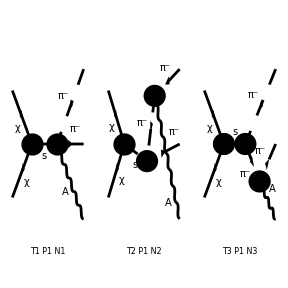

```mathematica
(* x + xbar -> pi + pi + gamma *)
dndeππ=HazmaComputeDNDE[{statex,statexbar},{stateπp,stateπm},Q,Paint->True];
```